```mathematica
<<"mechanisms`"
```

C compilation failed. Using MVM code instead.

## Defining Functions

### Creating objects

```mathematica
swelledUnitCell[height_,spacing_,displacement_]:=Module[{tempAngle,tempUnitCell},
tempUnitCell=framework[{{0,-height},{-displacement,0},{0,height},{-displacement+spacing,0}},
{Property[spring[{1,2}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,3}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,4}],{"stiffness"->springStiffness,MeshCellStyle->Blue}],
joint[1],joint[3],
Property[angleJoint[{1,2,3}],{"angularStiffness"->torsionalStiffness,"angle"->restingAngle}]},
MeshCellLabel->{0->"Index"}];
tempAngle=First[turningAngle[mechanismPositions[tempUnitCell],{{1,2,3}}]];
tempUnitCell/. restingAngle->tempAngle]
```

```mathematica
unswelledUnitCell[height_,spacing_]:=
framework[{{0,-height},{0,0},{0,height},{spacing,0}},
{Property[spring[{1,2}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,3}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,4}],{"stiffness"->springStiffness,MeshCellStyle->Blue}],
joint[1],joint[3]},
MeshCellLabel->{0->"Index"}]
```

```mathematica
swelledChain[height_,spacing_,displacement_,length_]:=deleteVertices[tesselateMechanism[swelledUnitCell[height,spacing,displacement],{{spacing,0},{0,0}},{length,1}
],{3length+1}]
```

```mathematica
unswelledChain[height_,spacing_,length_]:=deleteVertices[tesselateMechanism[unswelledUnitCell[height,spacing],{{spacing,0},{0,0}},{length,1}
],{3length+1}]
```

```mathematica
flipFlop[height_,width_]:=framework[{{0,0},{width,0},{width/2,height/4},{0,height/2},{width,height/2},{width/2,3height/4},{0,height},{width,height}},
{Property[rigidBar[{1,2}],{MeshCellStyle->Red }],
Property[rigidBar[{1,3}],{MeshCellStyle->Red }],
Property[rigidBar[{1,4}],{MeshCellStyle->Red }],
Property[rigidBar[{2,3}],{MeshCellStyle->Red }],
Property[rigidBar[{2,5}],{MeshCellStyle->Red }],
Property[rigidBar[{3,6}],{MeshCellStyle->Red }],
Property[rigidBar[{4,5}],{MeshCellStyle->Red }],
Property[rigidBar[{4,7}],{MeshCellStyle->Red }],
Property[rigidBar[{5,8}],{MeshCellStyle->Red }],
Property[rigidBar[{6,7}],{MeshCellStyle->Red }],
Property[rigidBar[{6,8}],{MeshCellStyle->Red }],
Property[rigidBar[{7,8}],{MeshCellStyle->Red }],
joint[4],joint[5]},
MeshCellLabel->{0->"Index"}
]
```

```mathematica
verticalUnitCell[height_,spacing_,displacement_]:=Module[{tempAngle,tempUnitCell},
tempUnitCell=framework[{{-height,0},{0,displacement},{height,0},{0,displacement+spacing}},
{Property[spring[{1,2}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,3}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,4}],{"stiffness"->springStiffness,MeshCellStyle->Blue}],
joint[1],joint[3],
Property[angleJoint[{1,2,3}],{"angularStiffness"->torsionalStiffness,"angle"->restingAngle}]},
MeshCellLabel->{0->"Index"}];
tempAngle=First[turningAngle[mechanismPositions[tempUnitCell],{{1,2,3}}]];
tempUnitCell/. restingAngle->tempAngle]
```

```mathematica
verticalChain[height_,spacing_,displacement_,length_]:=deleteVertices[tesselateMechanism[verticalUnitCell[height,spacing,displacement],{{0,0},{0,spacing}},{1,length}
],{3length+1}]
verticalChain[2,2,1/4,3]
```

### Modifying objects

```mathematica
removeBeam[chain_,n_]:=
deleteVertices[chain,{3n,3n-1,3n-2}]
```

```mathematica
insertFlipFlop[chain_,height_,spacing_,displacement_,location_]:=Module[{temp1,temp2},
temp1=removeBeam[chain,location];
temp2=joinMechanism[temp1,
framework[{{(location-1)*spacing-displacement,0},{(location-1)*spacing-displacement+(2/3)*spacing,0},{(location+1)*spacing-displacement-(2/3)*spacing,0},{(location+1)*spacing-displacement,0}},
{Property[rigidBar[{1,2}],{MeshCellStyle->Red }],
Property[rigidBar[{3,4}],{MeshCellStyle->Red }]},MeshCellLabel->{0->"Index"}]];
joinMechanism[temp2,#+{spacing*(location-1)-displacement+(2/3)*spacing,-height*2}&/@flipFlop[height*2,(2/3)*spacing]]
]
```

```mathematica
joinFlipFlopTL[chain_,height_,spacing_,displacement_,length_]:=Module[{temp1},
temp1=joinMechanism[chain,framework[{{length*spacing-displacement,0},{length*spacing-displacement+(2/3)*spacing,0}}, 
{Property[rigidBar[{1,2}],{MeshCellStyle->Red }]},
MeshCellLabel->{0->"Index"}]];
joinMechanism[temp1,#+{spacing*length-displacement+(2/3)*spacing,-height*2}&/@flipFlop[height*2,(2/3)*spacing]]
]
```

```mathematica
joinFlipFlopTR[chain_,height_,spacing_,displacement_,length_]:=Module[{temp1},
temp1=joinMechanism[chain,framework[{{spacing-displacement,0},{spacing-displacement-(2/3)*spacing,0}}, 
{Property[rigidBar[{1,2}],{MeshCellStyle->Red }]},
MeshCellLabel->{0->"Index"}]];
joinMechanism[temp1,#+{spacing-displacement-(4/3)*spacing,-height*2}&/@flipFlop[height*2,(2/3)*spacing]]
]
```

```mathematica
joinFlipFlopBL[chain_,height_,spacing_,displacement_,length_]:=Module[{temp1},
temp1=joinMechanism[chain,framework[{{length*spacing-displacement,0},{length*spacing+-displacement+(2/3)*spacing,0}}, 
{Property[rigidBar[{1,2}],{MeshCellStyle->Red }]},
MeshCellLabel->{0->"Index"}]];
joinMechanism[temp1,#+{spacing*length-displacement+(2/3)*spacing,0}&/@flipFlop[height*2,(2/3)*spacing]]
]
```

```mathematica
joinFlipFlopBR[chain_,height_,spacing_,displacement_,length_]:=Module[{temp1},
temp1=joinMechanism[chain,framework[{{spacing-displacement,0},{spacing-displacement-(2/3)*spacing,0}}, 
{Property[rigidBar[{1,2}],{MeshCellStyle->Red }]},
MeshCellLabel->{0->"Index"}]];
joinMechanism[temp1,#+{spacing-displacement-(4/3)*spacing,0}&/@flipFlop[height*2,(2/3)*spacing]]]
```

## testing

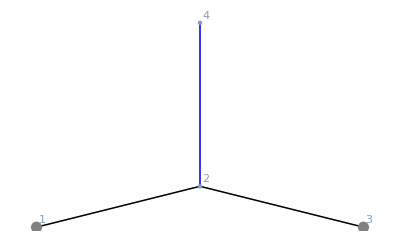

```mathematica
verticalUnitCell[height_,spacing_,displacement_]:=Module[{tempAngle,tempUnitCell},
tempUnitCell=framework[{{-height,0},{0,displacement},{height,0},{0,displacement+spacing}},
{Property[spring[{1,2}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,3}],{"stiffness"->beamStiffness,MeshCellStyle->Black}],
Property[spring[{2,4}],{"stiffness"->springStiffness,MeshCellStyle->Blue}],
joint[1],joint[3],
Property[angleJoint[{1,2,3}],{"angularStiffness"->torsionalStiffness,"angle"->restingAngle}]},
MeshCellLabel->{0->"Index"}];
tempAngle=First[turningAngle[mechanismPositions[tempUnitCell],{{1,2,3}}]];
tempUnitCell/. restingAngle->tempAngle]
verticalUnitCell[1,1,1/4]
```

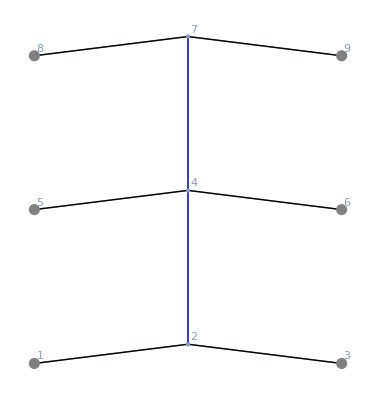

```mathematica
verticalChain[height_,spacing_,displacement_,length_]:=deleteVertices[tesselateMechanism[verticalUnitCell[height,spacing,displacement],{{0,0},{0,spacing}},{1,length}
],{3length+1}]
verticalChain[2,2,1/4,3]
```